# Stochastic processes

We examine a few stochastic processes, and practice with random variables.

```mathematica
ClearAll["Global`*"]
```

Generate a pseudorandom real number between 0 and 2π.

```mathematica
RandomReal[{0,2Pi}]
```

2.82534

#### Random walk (first order)

We create a random walk function which takes in initial conditions, number of time-steps, and distance traveled per time-step.

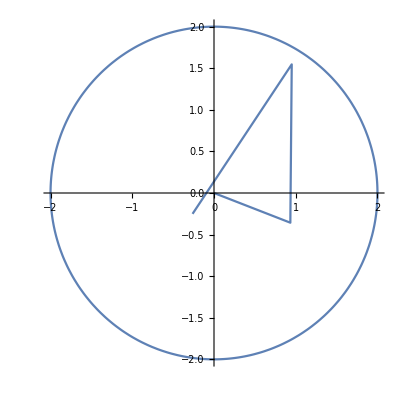

```mathematica
RandomWalk[init_,steps_,d_]:=Module[{},
solutions={init};
direction[x0_,t_]:=x0+{{Cos[t],-Sin[t]},{Sin[t],Cos[t]}}.{{d},{0}};
n=2;
While[n≤steps,
currX=solutions[[n-1]];
solutions=Append[solutions,direction[currX,RandomReal[{0,2Pi}]]];
n+=1;
];
solutions
];
With[{n=4,r=2},Show[ListPlot[
Level[RandomWalk[{{0},{0}},n,1][[#]],{-1}]&/@Range[n],
Joined->True,
AspectRatio->1,
PlotRange->{{-r,r},{-r,r}}],
ParametricPlot[r{Cos[t],Sin[t]},{t,0,2Pi}]
]
]
```